## Inverse Tone-Mapping Exploration of inverse tone mapping operators for our “Unreal” and ACES operators. Source image

```mathematica
ClearAll["Global`*"]
```

```mathematica
image=Image[-Graphics-]
```

-Graphics-

## Operators

```mathematica
(* Unreal Engine, modified to match ACES *)
unrealOp[x_,offset_,scale_] := x / (x + offset) * scale
unreal[x_] := unrealOp[x, 0.155,1.019]
inverseUnreal[x_]:=(-0.155*x)/(x - 1.019)
inverseUnrealLinearInput[x_]:=(-0.155*x^(1/2.2))/(x^(1/2.2) - 1.019)

(* ACES operator, for LDR and HDR *)
ACESop[x_,a_, b_, c_, d_, e_]:= (x*(a*x+b))/(x*(c*x+d)+e)
(* ACES sRGB *)
linearACES[x_] := Clip[ACESop[x, 2.51, 0.03, 2.43, 0.59, 0.14],{0,1}]
ACES[x_]:=linearACES[x]^(1/2.2)

identityUnreal[x_]=unreal[inverseUnreal[x]];
identityUnrealLinearInput[x_]=unreal[inverseUnrealLinearInput[x]];
identityACES[x_]=ACES[inverseUnreal[x]];
identityACESLinearInput[x_]=ACES[inverseUnrealLinearInput[x]];
```

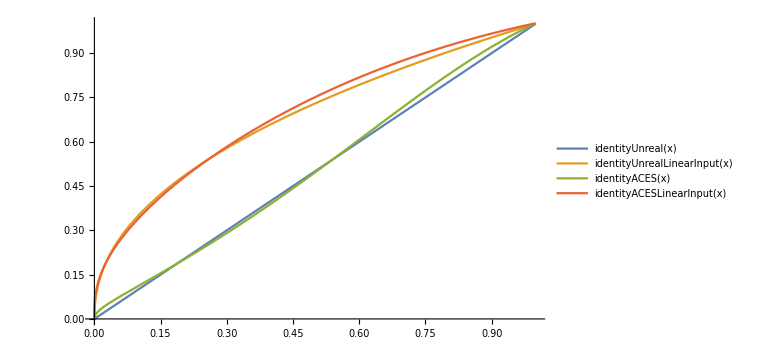

```mathematica
Plot[{ 
identityUnreal[x],
identityUnrealLinearInput[x],
identityACES[x],
identityACESLinearInput[x]
}, {x, 0, 1},ImageSize->Large,PlotLegends->"Expressions"]
```

## Image results

```mathematica
imageIdentUnreal=ImageApply[identityUnreal,image]
```

-Graphics-

```mathematica
imageIdentACES= ImageApply[identityACES,image]
```

-Graphics-

## 5x difference

```mathematica
ImageMultiply[ImageDifference[imageIdentACES, imageIdentUnreal],5.0]
```

-Graphics-